```mathematica
Jp[n_,x_]:=Evaluate[D[BesselJ[n,x],x]]
H2p[n_,x_]:=Evaluate[D[HankelH2[n,x],x]]
```

```mathematica
Plot[f[1,x],{x,0,10}]
```

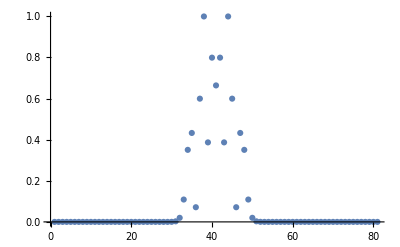

```mathematica
bn=Table[-I^n Jp[n,2Pi]/H2p[n,2Pi],{n,-40,40}];
ListPlot[Abs[bn],PlotRange->All]
```

```mathematica
bn
```

{{-10,7.44682×10^-6+0.00272888 ⅈ},{-9,-0.0198707+0.000394999 ⅈ},{-8,-0.0118437-0.108182 ⅈ},{-7,0.328344-0.122919 ⅈ},{-6,0.187307+0.390158 ⅈ},{-5,-0.0711729+0.00509151 ⅈ},{-4,-0.359613+0.479887 ⅈ},{-3,0.0253328-0.999358 ⅈ},{-2,0.149697+0.356774 ⅈ},{-1,0.480351+0.638792 ⅈ},{0,-0.441082-0.496517 ⅈ},{1,-0.480351-0.638792 ⅈ},{2,0.149697+0.356774 ⅈ},{3,-0.0253328+0.999358 ⅈ},{4,-0.359613+0.479887 ⅈ},{5,0.0711729-0.00509151 ⅈ},{6,0.187307+0.390158 ⅈ},{7,-0.328344+0.122919 ⅈ},{8,-0.0118437-0.108182 ⅈ},{9,0.0198707-0.000394999 ⅈ},{10,7.44682×10^-6+0.00272888 ⅈ}}